```mathematica
Θx[ns_]:=Table[Cos[(1+2k) π/ns],{k,0,ns-1}]
```

```mathematica
Θy[ns_]:=Table[Sin[(1+2k) π/ns],{k,0,ns-1}]
```

```mathematica
Θx[ 4]
```

{1/(√2),-1/(√2),-1/(√2),1/(√2)}

```mathematica
Θy[4]
```

{1/(√2),1/(√2),-1/(√2),-1/(√2)}

```mathematica
yc=Θy[3];
xc=Θx[3];
yc1=Θy[4];
xc1=Θx[4];
xc2=Θx[6];
yc2=Θy[6];
xc3=Θx[8];
yc3=Θy[8];
xy=Thread[{xc,yc}];
xy1=Thread[{xc1,yc1}];
xy2=Thread[{xc2,yc2}];
xy3= Thread[{xc3,yc3}];
```

```mathematica
mostra={Circle[#,.12]}&/@xy;
mostra1={Circle[#,.12]}&/@xy1;
mostra2={Circle[#,.12]}&/@xy2;
mostra3 ={Circle[#,.12]}&/@xy3;
```

```mathematica
o0=Graphics[mostra,AspectRatio->Automatic,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}];
o1=Graphics[mostra1,AspectRatio->Automatic,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}];
o2=Graphics[mostra2,AspectRatio->Automatic,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}];
o3=Graphics[mostra3,AspectRatio->Automatic,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}];
```

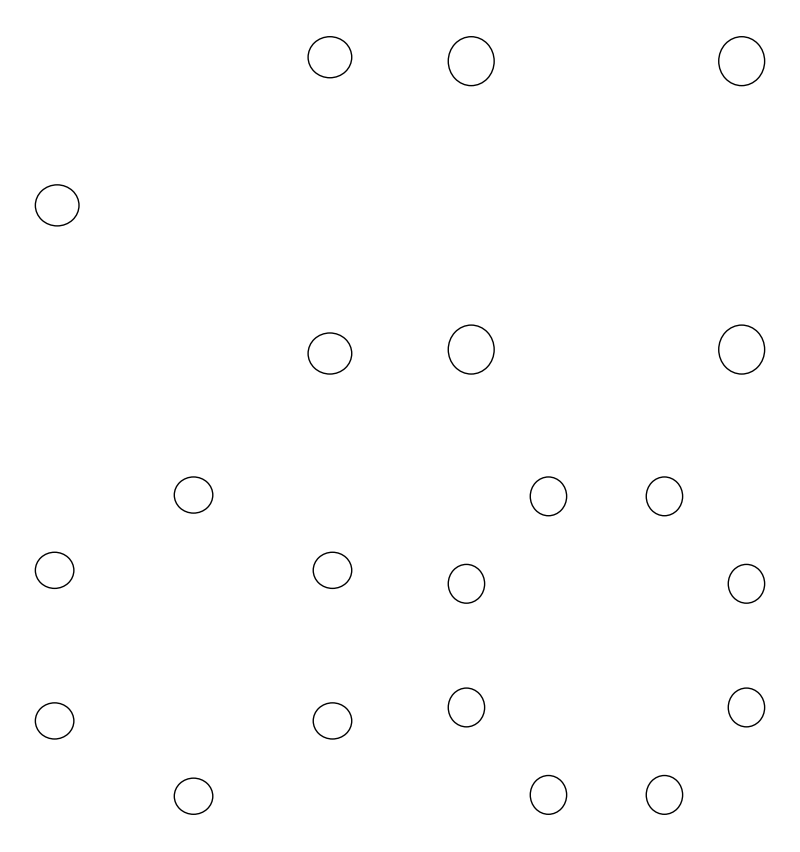

```mathematica
GraphicsGrid[{{o0,o1},{o2,o3}}]
```